# The integrate-and-fire model of neurons.

We'll start by looking at the most basic form of the integrate-and-fire model:

I(t) = (u(t))/R+ C du/dt,

where I(t) is the current, u(t) is the membrane potential, R is the cell resistance and C the cell capacitance.

Multiplying both sides by R and introducing the time constant τ = R C of the "leaky integrator", we get

τ du/dt = - u(t) + R I(t).

If we take the reset potential of the neuron to be u_r = 0, the last spike at t = 0 and assume that I(t) = I_0 = constant, then we may solve for u(t) analytically

```mathematica
FullSimplify[DSolve[{τ D[u[t],t]==-u[t] + R I0, u[0]==0},u[t],t]]
```

{{u[t]→(1-ⅇ^(-t/τ)) I0 R}}

Since the potential goes back to the reset potential after each time u(t) = u_threshold, the time interval between spikes is obtained by solving the above equation for t:

```mathematica
FullSimplify[Solve[Subscript[u, threshold]==(1-ⅇ^(-t/τ)) I0 R,t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-τ Log[1-u_threshold/(I0 R)]}}

Now let's assume a time-dependent input current, I(t).  Let's also assume that the reset potential is some finite value u_r, and that the last spike occurred at t = t̃.  Then

```mathematica
FullSimplify[DSolve[{τ D[u[t],t]==-u[t] + R I0[t], u[0]==Subscript[U, reset]},u[t],t]]
```

{{u[t]→ⅇ^(-t/τ) (-∫_1^0 (ⅇ^(K[1]/τ) R I0[K[1]])/τ ⅆK[1]+∫_1^t (ⅇ^(K[1]/τ) R I0[K[1]])/τ ⅆK[1]+U_reset)}}

## Rotter & Diesmann

In Rotter and Diesmann's 1999 paper, they discuss the following form of linear differential equation:
(ⅆ y(t))/(ⅆ t) = A y(t) + x(t)

with initial value y(s).  It has a solution of

y(t) = e^(A(t-s))y(s) + ∫e^(A(t-τ))x(τ) ⅆτ,

where the integral goes from s to t.

We can verify that right away:

```mathematica
Collect[FullSimplify[DSolve[{Y'[t]==A Y[t] + x[t],Y[s]==Ys},Y[t],t]],Ys]
```

{{Y[t]→ⅇ^(A (-s+t)) Ys+ⅇ^(A s+A (-s+t)) (-∫_1^s ⅇ^(-A K[1]) x[K[1]]ⅆK[1]+∫_1^t ⅇ^(-A K[1]) x[K[1]]ⅆK[1])}}

Which is indeed the expression quoted by Rotter & Diesmann.

Now, using the above analytical expression, we may write our own model of integrate-and-fire neurons with exponentially decaying post-synaptic current, with the help of the Rotter & Diesmann paper.  Let's begin with the basic dynamical equation:

τ_m (ⅆV(t))/ⅆt = E_L - V(t) + R_m I(t), 

which can be written as 

(ⅆV(t))/ⅆt = -1/τ_m V(t) + (E_L + R_m I(t))/τ_m,

from which one might make the identification that A = -1/τ_m and x(t) = (E_L + R_m I(t))/τ_m.  So the solution would be 

V(t) = e^(-1/τ_m(t-s))V(s) + ∫ e^(-1/τ_m(t-τ))(E_L + R_m I(τ))/τ_mⅆτ

where the integration goes from s to t.

Let's try to integrate the second term, assuming an I(t) that is the sum of an exponentially decreasing postsynaptic current I_e[t] and a constant input/background current I_c

```mathematica
Ie[Isyn_,τ_,t_]:= Isyn Exp[-t/τ]
```

```mathematica
EL = 0;
```

```mathematica
FullSimplify[Integrate[Exp[(-(t-d))/Subscript[τ, m]](EL+Subscript[R, m] (Ic+Ie[Isyn,Subscript[τ, ex],d]))/Subscript[τ, m],{d,s,t}]]
```

R_m (Ic-ⅇ^((s-t)/τ_m) Ic+((ⅇ^(-t/τ_ex)-ⅇ^(-s/τ_ex+(s-t)/τ_m)) Isyn τ_ex)/(τ_ex-τ_m))

```mathematica
Collect[FullSimplify[Subscript[R, m] (Ic-ⅇ^((s-t)/Subscript[τ, m]) Ic+((ⅇ^(-t/Subscript[τ, ex])-ⅇ^(-s/Subscript[τ, ex]+(s-t)/Subscript[τ, m])) Isyn Subscript[τ, ex])/(Subscript[τ, ex]-Subscript[τ, m]))],{Isyn,Ic}]
```

(1-ⅇ^((s-t)/τ_m)) Ic R_m+((ⅇ^(-t/τ_ex)-ⅇ^(-s/τ_ex+(s-t)/τ_m)) Isyn R_m τ_ex)/(τ_ex-τ_m)

```mathematica
(1-ⅇ^((s-t)/Subscript[τ, m])) Ic Subscript[R, m]+((ⅇ^(-t/Subscript[τ, ex])-ⅇ^(-s/Subscript[τ, ex]+(s-t)/Subscript[τ, m])) Isyn Subscript[R, m] Subscript[τ, ex])/(Subscript[τ, ex]-Subscript[τ, m])/.{s->0,t->h,Subscript[R, m]->Subscript[τ, m]/C}
```

((1-ⅇ^(-h/τ_m)) Ic τ_m)/C+((ⅇ^(-h/τ_ex)-ⅇ^(-h/τ_m)) Isyn τ_ex τ_m)/(C (τ_ex-τ_m))

```mathematica
Limit[(Exp[-h/(tau+dt)] - Exp[-h/tau])/dt, dt->0]
```

(ⅇ^(-h/tau) h)/tau^2

Taking everything we've derived thus far, with s = 0, t = h, R_m = τ_m/C and Ic = I_const, we arrive at what is programmed in Nest's iaf_psc_exp model (with an added part accounting for inhibitory synaptic current):

V_m(t+h) = V_m(t) e^(-h/τ_m) + I_(syn,ex) (τ_m e^(-h/τ_ex))/(C (1-τ_m/τ_ex))[1 - e^(h/τ_ex-h/τ_m)] + I_(syn,in)(τ_m e^(-h/τ_in))/(C (1-τ_m/τ_in))[1 - e^(h/τ_in-h/τ_m)] + I_const τ_m/C(1 - e^(-h/τ_m))

```mathematica
FullSimplify[Series[Subscript[τ, m] Exp[-h/Subscript[τ, ex]](1 - Exp[h/Subscript[τ, ex]-h/Subscript[τ, m]]),{h,0,3}]]
```

(1-τ_m/τ_ex) h+(-1/(2 τ_m)+τ_m/(2 τ_ex^2)) h^2+(1/(6 τ_m^2)-τ_m/(6 τ_ex^3)) h^3+O[h]^4

## Verify NEST

Let's see if we could reproduce the results of NEST here in Mathematica.  We can start by assuming the simplest case: I(t) = I_const.  Then, we may directly compute the amount of time Δt it takes to ramp the membrane potential from an initial condition E_L to V_threshold, and then compute the firing rate = 1/(Δt + t_(ref,absolute)).

So let's directly solve the first order differential equation in Mathematica:
(ⅆV(t))/ⅆt = -1/τ_m V(t) + (E_L + R_m I(t))/τ_m
with
I(t) = I_const + I_syn e^(-t/τ_ex).

```mathematica
Collect[FullSimplify[DSolve[{Subscript[τ, m] D[V[t],t]==EL - V[t] + Subscript[R, m] (Ic + Isyn Exp[-t/Subscript[τ, ex]]),V[s]== EL},V[t],t]],Exp[-t/Subscript[τ, m]]]/.s->0
```

{{V[t]→((EL+(Ic-ⅇ^(-t/τ_m) Ic+(ⅇ^(-t/τ_ex)-ⅇ^(-t/τ_m)) Isyn) R_m) τ_ex+(-EL+(-1+ⅇ^(-t/τ_m)) Ic R_m) τ_m)/(τ_ex-τ_m)}}

```mathematica
V[t_,EL_,Ic_,Rm_,τm_,Isyn_,τex_]:=1/(τex-τm)((EL+(Ic-ⅇ^(-t/τm) Ic+(ⅇ^(-t/τex)-ⅇ^(-t/τm)) Isyn) Rm) τex+(-EL+(-1+ⅇ^(-t/τm)) Ic Rm) τm)
```

```mathematica
Vth = -55 10^-3;
EL = -70 10^-3;
Ic = 0 10^-9;
τm = 10 10^-3;
trefabs = 2 10^-3;
Cm = 250 10^-12;
Rm = τm/Cm;
Isyn = 3 10^-9;
τex=2 10^-3;
```

What if a neuron is only receiving the exponentially-decaying post-synaptic current from some feed neuron?  Here's how it goes, assuming I_syn is 3 nA initially:

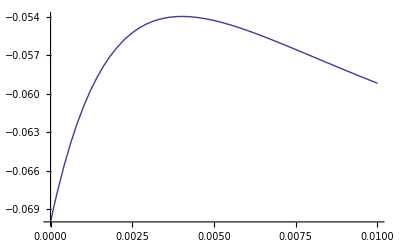

```mathematica
Plot[V[t,EL,Ic,Rm,τm,Isyn,τex],{t,0,0.01}]
```

```mathematica
FindRoot[V[t,EL,Ic,Rm,τm,Isyn,τex]==Vth,{t,0.0027}]
```

{t→0.00262535}

```mathematica
1/(0.00596734736955585+trefabs)
```

125.512

Now we solve for the amount of time it takes to reach V_th, if I_syn = 0:

```mathematica
ClearAll[Vth,EL,Ic,Rm,τm,Isyn,τex,trefabs,Cm]
```

```mathematica
Collect[FullSimplify[EL+1/(Subscript[τ, ex]-Subscript[τ, m])((Ic-ⅇ^((s-t)/Subscript[τ, m]) Ic+(ⅇ^(-t/Subscript[τ, ex])-ⅇ^(-s/Subscript[τ, ex]+(s-t)/Subscript[τ, m])) Isyn) Subscript[R, m] Subscript[τ, ex]+(-1+ⅇ^((s-t)/Subscript[τ, m])) Ic Subscript[R, m] Subscript[τ, m])]/.{Isyn->0,s->0},Exp[-t/Subscript[τ, m]]]
```

EL+(Ic R_m τ_ex)/(τ_ex-τ_m)-(Ic R_m τ_m)/(τ_ex-τ_m)+ⅇ^(-t/τ_m) (-(Ic R_m τ_ex)/(τ_ex-τ_m)+(Ic R_m τ_m)/(τ_ex-τ_m))

```mathematica
Solve[Subscript[V, th]== EL+(Ic Subscript[R, m] Subscript[τ, ex])/(Subscript[τ, ex]-Subscript[τ, m])-(Ic Subscript[R, m] Subscript[τ, m])/(Subscript[τ, ex]-Subscript[τ, m])+ⅇ^(-t/Subscript[τ, m]) (-(Ic Subscript[R, m] Subscript[τ, ex])/(Subscript[τ, ex]-Subscript[τ, m])+(Ic Subscript[R, m] Subscript[τ, m])/(Subscript[τ, ex]-Subscript[τ, m])),t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-Log[-(-EL-Ic R_m+V_th)/(Ic R_m)] τ_m}}

```mathematica
Subscript[Δt, const][Vth_,EL_,Ic_,Rm_,τm_]:= -Log[-(-EL-Ic Rm+Vth)/(Ic Rm)] τm
```

```mathematica
Subscript[FiringRate, const][Vth_,EL_,Ic_,Rm_,τm_,τref_]:= (1)/(Subscript[Δt, const][Vth,EL,Ic,Rm,τm]+ τref  )
```

Here are the relevant parameters that will be used in NEST's iaf_psc_exp model.  Keep in mind that the potentials are in mV, times in ms, current in pA and capacitance in pF.:

```mathematica
Vth = -55 10^-3;
EL = -70 10^-3;
Ic = 0.5 10^-9;
τm = 10 10^-3;
trefabs = 2 10^-3;
Cm = 250 10^-12;
Rm = τm/Cm;
```

```mathematica
Subscript[FiringRate, const][Vth,EL,Ic,Rm,τm,trefabs]//N
```

63.04

```mathematica
Subscript[Δt, const][Vth,EL,Ic,Rm,τm]+ trefabs//N
```

0.0158629

```mathematica
VData = Import["/Users/CW/Desktop/nest-1.9.8401-2/LSM/vdata-Ic500.dat","Table"];
```

```mathematica
VData[[138,3]]
VData[[297,3]]
VData[[456,3]]
VData[[297,2]]-VData[[138,2]]
VData[[456,2]]-VData[[297,2]]
```

-55.032

-55.032

-55.032

15.9

15.9

```mathematica
1/0.0159
```

62.8931

## Verify NEST - Continued

A simple NEST test of the iaf_psc_exp model would be hooking up a feed neuron to a receiving neuron, injecting an I_const (say, 0.5 nA) into the feed neuron while setting the amplitude of the connection (say, I_syn=3nA), and look at the shift in firing times (don't forget to account for the "delay" required in nest.Connect ).  You'll see that the aforementioned Mathematica derivation agrees pretty well with NEST.

```mathematica
Data1 = Import["/Users/CW/Desktop/nest-1.9.8401-2/LSM/vdata-Ic500.dat","Table"];
Data2 = Import["/Users/CW/Desktop/nest-1.9.8401-2/LSM/vdata-Ic500-Isyn3000-receiver.dat","Table"];
```

```mathematica
{Data1[[1,2]],Data1[[1,3]]}
```

{0.1,-69.801}

```mathematica
Table[{Sin[n],Sin[2n]},{n,10}]
```

{{Sin[1],Sin[2]},{Sin[2],Sin[4]},{Sin[3],Sin[6]},{Sin[4],Sin[8]},{Sin[5],Sin[10]},{Sin[6],Sin[12]},{Sin[7],Sin[14]},{Sin[8],Sin[16]},{Sin[9],Sin[18]},{Sin[10],Sin[20]}}

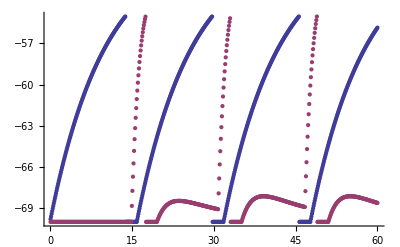

```mathematica
ListPlot[{Table[{Data1[[n,2]],Data1[[n,3]]},{n,1,600}],Table[{Data2[[n,2]],Data2[[n,3]]},{n,1,600}]}]
```

## Tsodyks Synapse

In Tsodyks & Markram 1997, we see synaptic resources being divided up into 3 modes: effective (E), inactive (I) and recovered (R).  The following rate equations decribe their relations:
dR/dt = I/τ_rec - U_SE R δ( t - t_AP)
dE/dt = - E/τ_inact + U_SE R δ( t - t_AP)
dI/dt = E/τ_inact - I/τ_rec
I + R + E = 1

The last equation is held true because E, I and R each denote the "fraction" of synaptic resources in that particular mode.  When an action potential (AP) hits the synapse, some chemical/electrical reaction occurs and we get a postsynaptic current.  The model argues that this Excitatory Postsynaptic Current (EPSC) is proportional to E, the fraction of "effective" synaptic resource.  The model further claims that E experiences an instantaneous jump at the moment the AP reaches the synapse, by converting a portion U_SE of R to E.  That is described by the U_SE R δ( t - t_AP ) term in dE/dt.  Of course, this implies a - U_SE R δ( t - t_AP ) term in dR/dt.  Furthermore, E spontaneously becomes "inactivated" into I with a time constant of τ_inact, while I spontaneously becomes "recovered" into R with a time constant τ_rec, which explain the rest of the model.

```mathematica
FullSimplify[DSolve[{D[Es[t],t]==(-Es[t])/Subscript[τ, ina],D[Is[t],t]==Es[t]/Subscript[τ, ina]-Is[t]/Subscript[τ, rec],D[Rs[t],t]==Is[t]/Subscript[τ, rec],D[Us[t],t]==(-Us[t])/Subscript[τ, facil],Is[0]==I0,Es[0]==E0,Rs[0]==R0,Us[0]==U0},{Es[t],Is[t],Rs[t],Us[t]},t]]
```

{{Es[t]→ⅇ^(-t/τ_ina) E0,Is[t]→(ⅇ^(-t (1/τ_ina+1/τ_rec)) (ⅇ^(t/τ_rec) E0 τ_rec+ⅇ^(t/τ_ina) (I0 τ_ina-(E0+I0) τ_rec)))/(τ_ina-τ_rec),Rs[t]→1/(τ_ina-τ_rec)((E0-ⅇ^(-t/τ_ina) E0+I0-ⅇ^(-t/τ_rec) I0+R0) τ_ina+ⅇ^(-t/τ_rec) (E0+I0) τ_rec-(E0+I0+R0) τ_rec),Us[t]→ⅇ^(-t/τ_facil) U0}}

```mathematica
Es[t_,τina_,E0_]:= E0 Exp[-t/τina]
Is[t_,τina_,τrec_,E0_,I0_]:= Exp[-t (1/τina+1/τrec)]/(τina-τrec) (Exp[t/τrec]E0 τrec + Exp[t/τina](I0 τina -(E0+I0)τrec))
Rs[t_,τina_,τrec_,E0_,I0_,R0_]:= 1/(τina-τrec)((E0-Exp[-t/τina]E0 + I0 - Exp[-t/τrec]I0+R0)τina +  Exp[-t/τrec](E0+I0)τrec-(E0+I0+R0)τrec)
Ts[t_,τina_,τrec_,E0_,I0_,R0_]:= Es[t,τina,E0]+Is[t,τina,τrec,E0,I0]+Rs[t,τina,τrec,E0,I0,R0]
Us[t_,τfacil_,U0_]:= U0 Exp[-t/τfacil]
```

In the NEST implementation of the tsodyks synapse, the following expression is used to express the evolution of R (or "x" in their code):

```mathematica
Rn1[t_,τina_,τrec_,E0_,I0_,R0_]:= 1 - I0 Exp[-t/τrec] - E0/(τrec-τina)(τrec Exp[-t/τrec]-τina Exp[-t/τina])
FullSimplify[Rn1[t,τina,τrec,E0,I0,R0]-Rs[t,τina,τrec,E0,I0,R0]]
```

1-E0-I0-R0

The above expression proves that the NEST implementation is the same as the one I've derived here, since E + I + R = 1.

So here's what E, I and R look like, if we start with E = 1, I = 0 and R = 0, and there's no subsequent action potential hitting the synapse

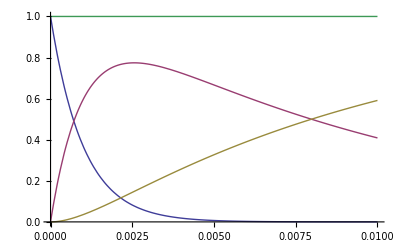

```mathematica
Plot[{Es[t,10^-3,1],Is[t,10^-3,10^-2,1,0],Rs[t,10^-3,10^-2,1,0,0],Ts[t,10^-3,10^-2,1,0,0]},{t,0,0.01}]
```

Now I shall use Mathematica to do a simple simulation to verify results obtained from NEST.  The simulation is based on injecting a causing current into a "feed" iaf_psc_exp neuron, which is in turn connected via a Tsodyks synapse to a receiver iaf_psc_exp neuron.  The feed neuron should fire regularly, but the receiver neuron may or may not fire due to synaptic dynamics.  

Let's begin by assuming that the neuronal parameters (C_m, τ_m, etc.) are defined as before, with an input current of 0.5 nA to the feed neuron.  This feed neuron hence should fire every 15.9 ms (accouting for the 1 ms synaptic delay).  The "weight" from this feed neuron is set to be 3000 pA.

We therefore only need to define just the parameters related to the Tsodyks synapse:

```mathematica
Vth = -55 10^-3;
EL = -70 10^-3;
τm = 10 10^-3;
trefabs = 2 10^-3;
Cm = 250 10^-12;
Rm = τm/Cm;

weight = 3000 10^-12;
τfac = 10^0;
τpsc = 2 10^-3;
τrec = 10^0;
U = 0.5;
τdelay = 10^-3;
```

With the initial values:

```mathematica
x =1;
y = 0;
u = 1;
```

It should be noted that, in the NEST implementaton of the Tsodyks synapse, the value of y ("Effective") is not the value passed to the post-synaptic integrator.  Instead, it's the instantaneous spike of y that is passed, which is u x.  In other words, the synapse code is called only at each spike

So here's how it works in NEST.  When a spike hits a synapse, the incremental change of y, δy = u x, is immediately determined.  Then, weight * δy is passed to the post-synaptic neuron to as an additive term to whatever post-synaptic current that is already present, and this new additive term will begin decaying as ~ weight * δy * e^((-(t-t_(new spike)))/τ_psc) once it enters the post-synaptic neuron.  When another spike occurs, the synapse is evaluated again, the time interval extracted to compute the current value of x, y, z and u, and a new value of δy is obtained, and the whole process recurs.

The Mathematica simulation will therefore go as follows:
1. Upon spike of the feed neuron, determine what the value of u after the delta-function increase is.  
2. After the 1 ms delay, start the exponentially decreasing post-synaptic current at weight * u.  Meanwhile, evolve x, y, z and u of the synapse.
3. Upon a new spike, determine what the instantaneous value of u is, based on the present values of x, y, z, etc.
4. super-impose the new value of weight * u to the current that's already being integrated at the receiver neuron and observe the potential change

We only need to compute the membrane potential response of the post-synaptic current (Ic = 0), assuming a spike occurs every 15.9 seconds:

```mathematica
Ic = 0;
δy = u x;
Isyn = 0;
tspike =Subscript[Δt, const][Vth,EL,0.5 10^-9,Rm,τm] + trefabs
```

0.0158629

```mathematica
Vms = Table[{0,0},{i,1,1000}];
Iss = Table[0,{i,1,1000}];
yss = Table[0,{i,1,1000}];
tss = Table[0,{i,1,1000}];
```

```mathematica
i = 0; 
t0 = tspike;
t =0;
tref = 3;
dt = 0.1/1000;
```

```mathematica
While[i<1000,
If[t0 ≥ tspike,
u = u + U (1 - u);
δy = u x;
y = y+δy;
Isyn = Isyn + weight δy;
x = x - δy;
E0 = y;
R0 = x; 
I0=1-x-y;
U0 = u;
t0=0;,
t0 = t0 + dt;x=Rs[t0,τpsc,τrec,E0,I0,R0];
y=Es[t0,τpsc,E0];
u=Us[t0,τfac,U0];yss[[i+1]]=y;];

Vms[[i+1,1]]=i; 
t = t + dt; 
Vms[[i+1,2]]= V[t,EL,Ic,Rm,τm,Isyn,τpsc];

If[tref≤trefabs,
tref=tref+0.1/1000;Vms[[i+1,2]]=EL;t=0;Isyn=Ie[Isyn,τpsc,dt];,{}];
If[Vms[[i+1,2]]≥Vth,Vms[[i+1,2]]=EL;tref=0;Isyn=Ie[Isyn,τpsc,t];,{} ];

Iss[[i+1]]=Isyn;
tss[[i+1]]=t;
i++]
```

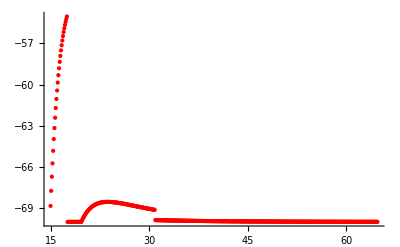

```mathematica
Plot1=
 ListPlot[Table[{Vms[[n,1]]/10 +14.9,Vms[[n,2]]*1000},{n,1,500}],PlotStyle->{Red,PointSize[Medium]},PlotRange->All]
```

Now that I have the functional form of the "Effective", "Inactive" and "Recovered" resources, let's try to do something that could also be done in NEST.  How would I test this?

We can begin by connecting a feed neuron to a receiving neuron, both iaf_psc_exp neurons.  The feed neuron would fire ONCE, releasing an exponentially decaying post-synaptic current I_syn(t) into the receiving neuron.  The current actually received in the receiving neuron would depend on the time-dependent dynamics of the tsodyks synapse that forms the connection between the two neurons.  

It should be noted that, in this test, t

```mathematica
VDataTemp1 = Import[
"/Users/CW/Desktop/nest-1.9.8401-2/LSM/voltmeter-3-0.dat","Table"];
```

```mathematica
VDataTemp2 = Import[
"/Users/CW/Desktop/nest-1.9.8401-2/LSM/voltmeter-4-0.dat","Table"];
```

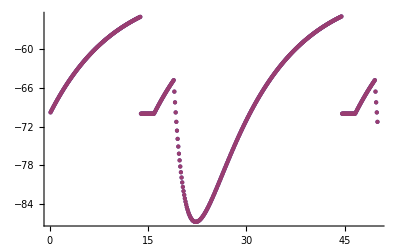

```mathematica
ListPlot[{Table[{VDataTemp1[[n,2]],VDataTemp1[[n,3]]},{n,1,500}],Table[{VDataTemp2[[n,2]],VDataTemp2[[n,3]]},{n,1,500}]},PlotRange->All]
```

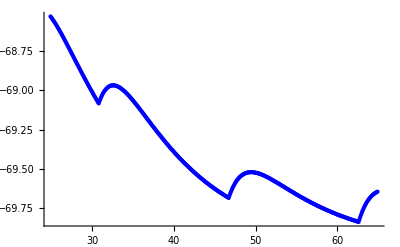

```mathematica
Plot2 =ListPlot[{Table[{VDataTemp1[[n,2]],VDataTemp1[[n,3]]},{n,249,649}]},PlotRange->All,PlotStyle->{Blue,PointSize[Medium]}]
```

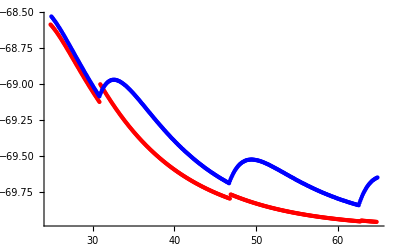

```mathematica
Show[Plot1,Plot2]
```

Here's Eq. 20 of Prof. Herz's notes on the Tsodyks synaptic model:

```mathematica
En1[t_,En_,τina_,Use_,In_,τrec_]:= En Exp[-t/τina] + Use(1 - In Exp[-t/τrec]-En/(τrec - τina)(τrec Exp[-t/τrec]-τina Exp[-t/τina]))
```

```mathematica
En1[0,1,10^-2,0.99,0,10^0]//N
```

1.

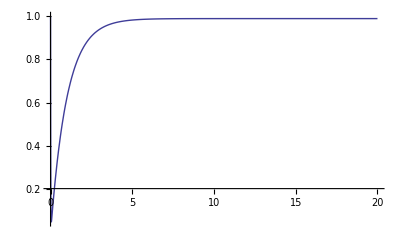

```mathematica
Plot[En1[t,1,10^-2,0.99,0,10^0],{t,0,20},PlotRange->All]
```

Here's what's actually implemented in the NEST code of tsydyks_synapse:

```mathematica
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
Integrate[PDF[NormalDistribution[μ,σ],x],{x,-∞,p},Assumptions->{Re[σ^2]>0}]
```

1/2 (√(1/σ^2) σ+Erf[(p-μ)/(√2 σ)])

```mathematica
Solve[r== Integrate[PDF[NormalDistribution[μ,σ],x],{x,-∞,p},Assumptions->{Re[σ^2]>0}],p]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→μ+√2 σ InverseErf[2 r-√(1/σ^2) σ]}}

```mathematica
PDF[GammaDistribution[α,β],x]
```

(ⅇ^(-x/β) x^(-1+α) β^-α)/Gamma[α]

```mathematica
Gamma[1]
```

1

```mathematica
Integrate[x Exp[-x/β] β^-1,{x,0,∞},Assumptions->Re[β]>0]
```

β

```mathematica
Integrate[PDF[GammaDistribution[α,β],x],{x,0,p},Assumptions->{Re[α]>0}]
```

(p^α (p/β)^-α β^-α (Gamma[α]-Gamma[α,p/β]))/Gamma[α]

## IAF with hyperpolarization

So, after hacking the NEST source code to introduce post-synaptic hyperpolarization into the iaf_psc_exp model, we need to verify that it works.

The new model has 2 new parameters, V_hyp_0 and τ_hyp.  The former gives the hyperpolarization of the membrane potential (relative to 0) and the latter is the enponential decay time constant.  

It should be noted that the hyperpolarization starts immediately after firing.  That is, it decays even during refractory period.  

To verify this code, we'll simply add the term 
V_hyp_0 exp[-t/τ_hyp]
to the evolving membrane potential, where V_hyp_0 is a negative value. 

Let's have constant incoming current: I(t) = I_const.  The evolution of the membrane potential is, as before:

```mathematica
V[t_,EL_,Ic_,Rm_,τm_,Isyn_,τex_]:=1/(τex-τm)((EL+(Ic-ⅇ^(-t/τm) Ic+(ⅇ^(-t/τex)-ⅇ^(-t/τm)) Isyn) Rm) τex+(-EL+(-1+ⅇ^(-t/τm)) Ic Rm) τm)
```

Now, accounting for the hyperpolarization, we have

```mathematica
Vnew[t_,EL_,Ic_,Rm_,τm_,Isyn_,τex_,trefabs_,Vhyp0_,τhyp_]:= V[t,EL,Ic,Rm,τm,Isyn,τex] + Vhyp0 Exp[(-(t+trefabs))/τhyp]
Vshift[t_,EL_,Ic_,Rm_,τm_,Isyn_,τex_]:= If[t<0,1000EL,1000 V[t/1000,EL,Ic,Rm,τm,Isyn,τex]]
VhypNew[t_,Vhyp0_,τhyp_]:=1000 Vhyp0 Exp[(-t/1000)/τhyp]
```

```mathematica
Vth = -55 10^-3;
EL = -70 10^-3;
Ic = 0.0 10^-9;
τm = 10 10^-3;
trefabs = 2 10^-3;
Cm = 15 250 10^-12;
Rm = τm/Cm;
Isyn = 15 3.8 10^-9;
τex=2 10^-3;
Vhyp0 = -35 10^-3;
τhyp = 4 10^-3;
τdelay = 1 10^-3;
```

```mathematica
FindRoot[Vnew[t,EL,Ic,Rm,τm,Isyn,τex,trefabs,Vhyp0,τhyp]==Vth,{t,0.0037}]
```

{t→0.00339365}

```mathematica
Vth = -55 10^-3;
EL = -70 10^-3;
Ic = 0.0 10^-9;
τm = 10 10^-3;
trefabs = 2 10^-3;
Cm = 250 10^-12;
Rm = τm/Cm;
Isyn = 80 49 10^-12;
τex=2 10^-3;
Vhyp0 = -15 10^-3;
τhyp = 3 10^-3;
τdelay = 5 10^-3;
```

```mathematica
Needs["PlotLegends`"]
```

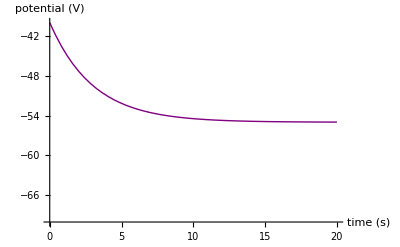

```mathematica
Plot1 =ShowLegend[Plot[1000 Vth-VhypNew[t+trefabs,Vhyp0,τhyp],{t,0,0.02 1000},PlotRange->{{0,0.02 1000},{-0.07 1000 ,-0.04 1000}},PlotStyle->{Purple},PlotStyle-> Thickness[0.010],BaseStyle->{FontFamily->"Helvetica",FontSize->12,Thick},AxesStyle->Directive[{Thickness[0.005]}],AxesLabel->{Style["time (s)",FontFamily->"Helvetica",FontSize->14],Style["potential (V)",FontFamily->"Helvetica",FontSize->14]}],{{{Graphics[{Thick,Purple,Line[{{0,0},{1,0}}]}],Style["Threshold Pot.",{FontFamily->"Helvetica",FontSize->12,Thick}]}},LegendPosition->{-0.4,0.01},LegendSize->{1.2,0.4},LegendShadow->None,LegendBorder->None,LegendTextOffset-> Automatic},LabelStyle->{FontFamily->"Helvetica",FontSize->14}]
```

```mathematica
Export["/Users/CW/Desktop/Refrac.jpg",Plot1,"JPEG",ImageResolution->120]
```

/Users/CW/Desktop/Refrac.jpg

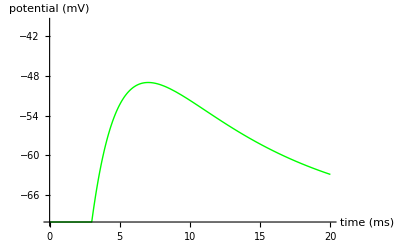

```mathematica
Plot2=ShowLegend[Plot[{Vshift[t-3/5 τdelay 1000,EL,Ic,Rm,τm,Isyn,τex]},{t,0,0.02 * 1000},PlotRange->{{0,0.02 * 1000},{-0.07*1000,-0.04 *1000}},PlotStyle->{Green},PlotStyle-> Thickness[0.010],BaseStyle->{FontFamily->"Helvetica",FontSize->12,Thick},AxesStyle->Directive[{Thickness[0.005]}],AxesLabel->{Style["time (ms)",FontFamily->"Helvetica",FontSize->14],Style["potential (mV)",FontFamily->"Helvetica",FontSize->14]}],{{{Graphics[{Thick,Green,Line[{{0,0},{1,0}}]}],Style["EPSP",{FontFamily->"Helvetica",FontSize->12,Thick}]}},LegendPosition->{-0.3,0.1},LegendSize->{1.0,0.4},LegendShadow->None,LegendBorder->None,LegendTextOffset-> Automatic},LabelStyle->{FontFamily->"Helvetica",FontSize->14}]
```

```mathematica
Export["/Users/CW/Desktop/MembraneP.jpg",Plot2,"JPEG",ImageResolution->120]
```

/Users/CW/Desktop/MembraneP.jpg

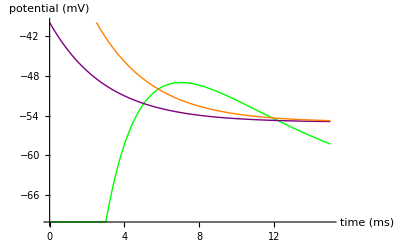

```mathematica
Plot3 = ShowLegend[Plot[{Vshift[t-3/5 τdelay 1000,EL,Ic,Rm,τm,Isyn,τex],1000Vth-VhypNew[t-0,Vhyp0,τhyp],1000Vth-VhypNew[t-2.5,Vhyp0,τhyp]},{t,0,0.015 * 1000},PlotRange->{{0,0.015 * 1000},{-0.07*1000,-0.04 *1000}},PlotStyle->{Green,Purple,Orange},PlotStyle-> Thickness[0.010],BaseStyle->{FontFamily->"Helvetica",FontSize->12,Thick},AxesStyle->Directive[{Thickness[0.005]}],AxesLabel->{Style["time (ms)",FontFamily->"Helvetica",FontSize->14],Style["potential (mV)",FontFamily->"Helvetica",FontSize->14]}],{{{Graphics[{Thick,Green,Line[{{0,0},{2,0}}]}],Style["EPSP",{FontFamily->"Helvetica",FontSize->12,Thick}]},{Graphics[{Thick,Purple,Line[{{0,0},{2,0}}]}],Style["0 lag",{FontFamily->"Helvetica",FontSize->12,Thick}]},{Graphics[{Thick,Orange,Line[{{0,0},{2,0}}]}],Style["2.5 ms lag",{FontFamily->"Helvetica",FontSize->12,Thick}]}},LegendPosition->{0.0,0.1},LegendSize->{1.0,0.4},LegendShadow->None,LegendBorder->None,LegendTextOffset-> Automatic},LabelStyle->{FontFamily->"Helvetica",FontSize->14}]
```

```mathematica
FindRoot[Vshift[t-3/5 τdelay 1000,EL,Ic,Rm,τm,Isyn,τex]==1000Vth-VhypNew[t,4.5 Vhyp0,τhyp],{t,9}]
```

{t→11.2013}

```mathematica
Export["/Users/CW/Desktop/Converging.jpg",Plot3,"JPEG",ImageResolution->120]
```

/Users/CW/Desktop/Converging.jpg

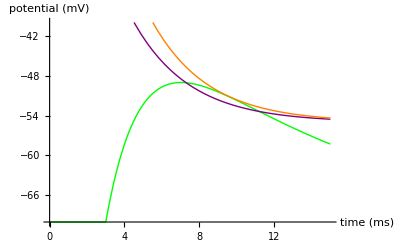

```mathematica
Plot4 = ShowLegend[Plot[{Vshift[t-3/5 τdelay 1000,EL,Ic,Rm,τm,Isyn,τex],1000Vth-VhypNew[t,4.5 Vhyp0,τhyp],1000Vth-VhypNew[t-1.0,4.5 Vhyp0,τhyp]},{t,0,0.015 * 1000},PlotRange->{{0,0.015 * 1000},{-0.07*1000,-0.04 *1000}},PlotStyle->{Green,Purple,Orange},PlotStyle-> Thickness[0.010],BaseStyle->{FontFamily->"Helvetica",FontSize->12,Thick},AxesStyle->Directive[{Thickness[0.005]}],AxesLabel->{Style["time (ms)",FontFamily->"Helvetica",FontSize->14],Style["potential (mV)",FontFamily->"Helvetica",FontSize->14]}],{{{Graphics[{Thick,Green,Line[{{0,0},{2,0}}]}],Style["EPSP",{FontFamily->"Helvetica",FontSize->12,Thick}]},{Graphics[{Thick,Purple,Line[{{0,0},{2,0}}]}],Style["0 lag",{FontFamily->"Helvetica",FontSize->12,Thick}]},{Graphics[{Thick,Orange,Line[{{0,0},{2,0}}]}],Style["1 ms lag",{FontFamily->"Helvetica",FontSize->12,Thick}]}},LegendPosition->{0.0,0.1},LegendSize->{1.0,0.4},LegendShadow->None,LegendBorder->None,LegendTextOffset-> Automatic},LabelStyle->{FontFamily->"Helvetica",FontSize->14}]
```

```mathematica
Export["/Users/CW/Desktop/ConvergingNot.jpg",Plot4,"JPEG",ImageResolution->120]
```

/Users/CW/Desktop/ConvergingNot.jpg

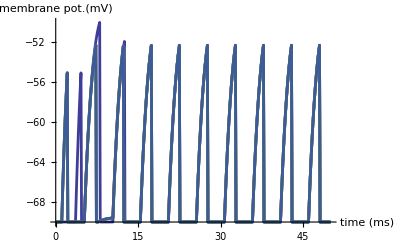

```mathematica
Data1 = Import["/Users/CW/Desktop/nest-1.9.8401-2/LSM/voltmeter-101-0.dat","Table"];
Data2 = Import["/Users/CW/Desktop/nest-1.9.8401-2/LSM/voltmeter-102-0.dat","Table"];
Data3 = Import["/Users/CW/Desktop/nest-1.9.8401-2/LSM/voltmeter-125-0.dat","Table"];
Data4 = Import["/Users/CW/Desktop/nest-1.9.8401-2/LSM/voltmeter-138-0.dat","Table"];
Data5 = Import["/Users/CW/Desktop/nest-1.9.8401-2/LSM/voltmeter-146-0.dat","Table"];
Plot5 = ListPlot[{Table[{Data1[[n,2]],Data1[[n,3]]},{n,1,500}],Table[{Data2[[n,2]],Data2[[n,3]]},{n,1,500}],Table[{Data3[[n,2]],Data3[[n,3]]},{n,1,500}],Table[{Data4[[n,2]],Data4[[n,3]]},{n,1,500}],Table[{Data5[[n,2]],Data5[[n,3]]},{n,1,500}]},PlotRange->All,Joined->True,PlotStyle->Thickness[0.005],AxesLabel->{Style["time (ms)",FontFamily->"Helvetica",FontSize->12],Style["membrane pot.(mV)",FontFamily->"Helvetica",FontSize->12]},BaseStyle->{FontFamily->"Helvetica",FontSize->12,Thick},AxesStyle->Directive[{Thickness[0.005]}]]
```

```mathematica
Export["/Users/CW/Desktop/DivergingPot.jpg",Plot5,"JPEG",ImageResolution->300]
```

/Users/CW/Desktop/DivergingPot.jpg

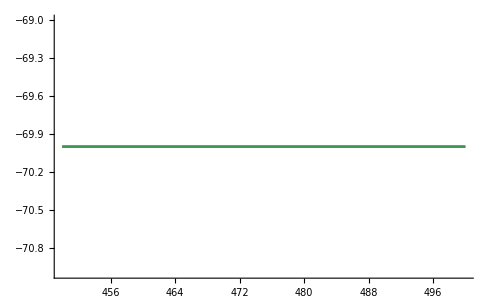

```mathematica
ListPlot[{Table[{Data1[[n,2]],Data1[[n,3]]},{n,4500,5000}],Table[{Data2[[n,2]],Data2[[n,3]]},{n,4500,5000}],Table[{Data3[[n,2]],Data3[[n,3]]},{n,4500,5000}],Table[{Data4[[n,2]],Data4[[n,3]]},{n,4500,5000}]},PlotRange->All,Joined->True,PlotStyle->Thickness[0.003]]
```

## Coherent Locking

I suspect that, when I set up my NEST examination of Coherent Locking, I use a parameter set that leads to phase shifts.  More specifically, the relative values of synaptic delay time and initial input jitter play an important role, as they impact which part of the membrane potential curve the intersect occurs.  

Based on Gerstner, van Hemmen and Cowen (1996).

The membrane potential is defined by the function V(), whereas the post-firing hyperpolarization is defined by Vhyp

```mathematica
Isynapse[t_,Isyn_,τex_]:= If[t<0,0,Isyn Exp[-t/τex]]
```

```mathematica
Vs[t_,s_,V0_,EL_,Ic_,Rm_,τm_,Isyn_,τex_,τdelay_,trefabs_]:= Exp[(-(t-s))/τm]V0 + NIntegrate[Exp[(-(t-τ))/τm] 1/τm(EL+Rm(Ic + Isynapse[τ-(τdelay-trefabs),Isyn,τex])),{τ,s,t}]
```

```mathematica
Vhyp[t_,Vhyp0_,τhyp_]:= Vhyp0 Exp[-t/τhyp]
```

```mathematica
Vth = -55 10^-3;
EL = -70 10^-3;
Ic = 500 10^-12;
τm = 10 10^-3;
trefabs = 2 10^-3;
Cm = 250 10^-12;
Rm = τm/Cm;
Isyn = -50*99* 10^-12  ;
τex=2 10^-3;
Vhyp0 = -25 10^-3;
τdelay = 8 10^-3;
τhyp = 5 10^-3;
```

```mathematica
FindRoot[Vs[t,0,EL,EL,Ic,Rm,τm,Isyn,τex,τdelay,trefabs]== Vth-Vhyp[t+trefabs,Vhyp0,τhyp],{t,0.03}]
```

NIntegrate::nlim: τ = t is not a valid limit of integration.

General::stop: Further output of NIntegrate :: "nlim" will be suppressed during this calculation.

{t→0.0309961}

```mathematica
(46.86-13.86) 10^-3 - trefabs
```

0.031

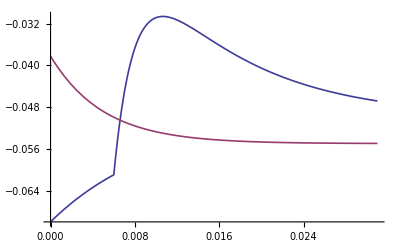

```mathematica
Figure0=Plot[{Vs[t,0,EL,EL,Ic,Rm,τm,Isyn,τex,τdelay,trefabs],Vth-Vhyp[t+trefabs,Vhyp0,τhyp]},{t,0,0.031},PlotRange->All,PlotStyle->Thickness[0.003]]
```

```mathematica
SomeData= Import["/Users/CW/Desktop/nest-1.9.8401-2/LSM/voltmeter-300-0.dat","Table"];
```

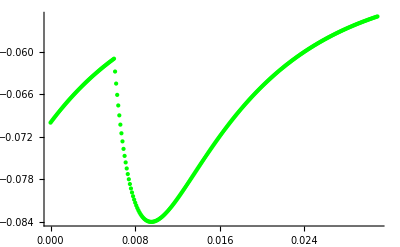

```mathematica
Figure1 = ListPlot[Table[{(SomeData[[n,2]]-SomeData[[9399,2]]) 10^-3,SomeData[[n,3]] 10^-3},{n,9399,9708}],PlotRange->All,PlotStyle->Green]
```

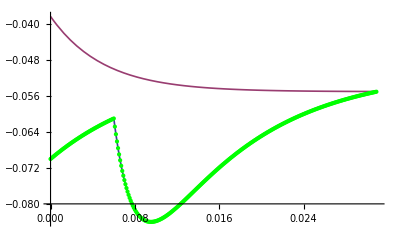

```mathematica
Show[Figure0,Figure1]
```

## I&F model with Conductance-based Adaptation

In Rotter and Diesmann's 1999 paper, they discuss the following form of linear differential equation:
(ⅆ y(t))/(ⅆ t) = A y(t) + x(t)

with initial value y(s).  It has a solution of

y(t) = e^(A(t-s))y(s) + ∫e^(A(t-τ))x(τ) ⅆτ,

where the integral goes from s to t.

We can verify that right away:

```mathematica
Collect[FullSimplify[DSolve[{Y'[t]==A Y[t] + x[t],Y[s]==Ys},Y[t],t]],Ys]
```

{{Y[t]→ⅇ^(A (-s+t)) Ys+ⅇ^(A s+A (-s+t)) (-∫_1^s ⅇ^(-A K[1]) x[K[1]]ⅆK[1]+∫_1^t ⅇ^(-A K[1]) x[K[1]]ⅆK[1])}}

Which is indeed the expression quoted by Rotter & Diesmann.

Now, using the above analytical expression, we may write our own model of integrate-and-fire neurons with exponentially decaying post-synaptic current, and a hyperpolarizing adaptation current with the help of the Rotter & Diesmann paper.  Let's begin with the basic dynamical equation:

τ_m (ⅆV(t))/ⅆt = E_L - V(t) + R_m I(t) - g(t) (V(t) - E_k) 

where g is some normalized unitless conductance of the [Ca^(2+)]-dependent K^+conductance, and E_k is yet another parameter related to K^+.  The equation can then be written as 

(ⅆV(t))/ⅆt = (-(1+g(t)))/τ_m V(t) + (E_L + R_m I(t) - g(t) E_k)/τ_m,

from which one might make the identification that A = (-(1+g(t)))/τ_m and x(t) = (E_L + R_m I(t) - g(t) E_k)/τ_m.  So the solution would be 

V(t) = e^((-(1+g(t)))/τ_m(t-s))V(s) + ∫ e^((-(1+g(t)))/τ_m(t-τ))(E_L + R_m I(τ) - g(t) E_k)/τ_mⅆτ

where the integration goes from s to t.

Let's try to integrate the second term, assuming an I(t) that is the sum of an exponentially decreasing postsynaptic current I_e[t] and a constant input/background current I_c

The evolution of g follows:
τ_adp dg/dt = -g
which is just

```mathematica
DSolve[{Subscript[τ, adp] D[g[t],t] ==  - g[t],g[0]==g0},g[t],t]
```

{{g[t]→ⅇ^(-t/τ_adp) g0}}

with the additional constraint that, after every spike, g = g + Δg, where Δg is some constant.

```mathematica
Ie[Isyn_,τ_,t_]:= Isyn Exp[-t/τ]
g[g0_,τ_,t_]:= g0 Exp[-t/τ]
```

```mathematica
EL = 0;
```

```mathematica
FullSimplify[Integrate[Exp[(-(1+g[g0,Subscript[τ, adp],t])(t-d))/Subscript[τ, m]](EL+Subscript[R, m] (Ic+Ie[Isynex,Subscript[τ, ex],d] + Ie[Isynin,Subscript[τ, in],d]) + g[g0,Subscript[τ, adp],d] Ek)/Subscript[τ, m],{d,s,t}]]
```

∫_s^t (ⅇ^(((-1-ⅇ^(-d/τ_adp) g0) (-d+t))/τ_m) (ⅇ^(-d/τ_adp) Ek g0+(Ic+ⅇ^(-d/τ_ex) Isynex+ⅇ^(-d/τ_in) Isynin) R_m))/τ_m ⅆd

Ok, let's try to solve this using DSolve, starting with the original equation:
τ_m (ⅆV(t))/ⅆt = E_L - V(t) + R_m I(t) - g(t) (V(t) - E_k)

```mathematica
FullSimplify[DSolve[{Subscript[τ, m] V'[t]==0 - V[t] + Subscript[R, m](Ic + Ie[Isynex,Subscript[τ, ex],t] + Ie[Isynin,Subscript[τ, in],t]) - g[t]( V[t] - Ek ), V[0] ==  V0},V[t],t]]
```

{{V[t]→(ⅇ^(-((1+g0) t)/τ_m) ((1+g0) τ_ex ((1+g0) (V0+g0 ((-1+ⅇ^(((1+g0) t)/τ_m)) Ek+V0)+((-1+ⅇ^(((1+g0) t)/τ_m)) Ic+(-1+ⅇ^(t (-1/τ_ex+(1+g0)/τ_m))) Isynex+(-1+ⅇ^(t (-1/τ_in+(1+g0)/τ_m))) Isynin) R_m) τ_in-(V0+g0 ((-1+ⅇ^(((1+g0) t)/τ_m)) Ek+V0)+((-1+ⅇ^(((1+g0) t)/τ_m)) Ic+(-1+ⅇ^(t (-1/τ_ex+(1+g0)/τ_m))) Isynex) R_m) τ_m)+τ_m (-(1+g0) (V0+g0 ((-1+ⅇ^(((1+g0) t)/τ_m)) Ek+V0)+((-1+ⅇ^(((1+g0) t)/τ_m)) Ic+(-1+ⅇ^(t (-1/τ_in+(1+g0)/τ_m))) Isynin) R_m) τ_in+(-Ek g0+V0+g0 V0-Ic R_m+ⅇ^(((1+g0) t)/τ_m) (Ek g0+Ic R_m)) τ_m)))/((1+g0) ((1+g0) τ_ex-τ_m) ((1+g0) τ_in-τ_m))}}

```mathematica
(Ek g)/(1+g)-(ⅇ^(((1+g) (s-t))/Subscript[τ, m]) Ek g)/(1+g)+Ic (Subscript[R, m]/(1+g)-(ⅇ^(((1+g) (s-t))/Subscript[τ, m]) Subscript[R, m])/(1+g))+Isynex ((ⅇ^(-t/Subscript[τ, ex]) Subscript[R, m] Subscript[τ, ex])/((1+g) Subscript[τ, ex]-Subscript[τ, m])-(ⅇ^(-s/Subscript[τ, ex]+((1+g) (s-t))/Subscript[τ, m]) Subscript[R, m] Subscript[τ, ex])/((1+g) Subscript[τ, ex]-Subscript[τ, m]))+Isynin ((ⅇ^(-t/Subscript[τ, in]) Subscript[R, m] Subscript[τ, in])/((1+g) Subscript[τ, in]-Subscript[τ, m])-(ⅇ^(-s/Subscript[τ, in]+((1+g) (s-t))/Subscript[τ, m]) Subscript[R, m] Subscript[τ, in])/((1+g) Subscript[τ, in]-Subscript[τ, m]))/.{s->0,t->h,Subscript[R, m]-> Subscript[τ, m]/Cm}
```

(Ek g)/(1+g)-(ⅇ^(-((1+g) h)/τ_m) Ek g)/(1+g)+Ic (τ_m/(Cm (1+g))-(ⅇ^(-((1+g) h)/τ_m) τ_m)/(Cm (1+g)))+Isynex ((ⅇ^(-h/τ_ex) τ_ex τ_m)/(Cm ((1+g) τ_ex-τ_m))-(ⅇ^(-((1+g) h)/τ_m) τ_ex τ_m)/(Cm ((1+g) τ_ex-τ_m)))+Isynin ((ⅇ^(-h/τ_in) τ_in τ_m)/(Cm ((1+g) τ_in-τ_m))-(ⅇ^(-((1+g) h)/τ_m) τ_in τ_m)/(Cm ((1+g) τ_in-τ_m)))

Taking everything we've derived thus far, with s = 0, t = h, R_m = τ_m/C and Ic = I_const, we arrive at what is programmed in Nest's iaf_psc_exp model (with an added part accounting for inhibitory synaptic current):

V_m(t+h) = V_m(t) e^(-h/τ_m) + I_(syn,ex) (τ_m e^(-h/τ_ex))/(C (1-τ_m/τ_ex))[1 - e^(h/τ_ex-h/τ)] + I_(syn,in)(τ_m e^(-h/τ_in))/(C (1-τ_m/τ_in))[1 - e^(h/τ_in-h/τ)] + I_const τ_m/C(1 - e^(-h/τ_m))

## I&F with adaptive hyperpolarizing potential

Here I take the original NEST code for iaf_psc_exp, and add an extension for adaptive hyperpolarization.  This adaptation model follows "Integrate-and-Fire model with adaptation are good enough" (2006) by Jolivet, Rauch, Luescher and Gerstner.  The adaptation changes the firing threshold such that, each time a spike is fired, the threshold is raised by an amount V_hyp_0.  This hyperpolarization potential then decays back to 0 with a time constant of tau_hyp.

If the neuron only fires once, then the hyperpolarization potential decays as:
V_hyp_0 exp[-t/τ_hyp],
 where V_hyp_0 is a negative value.  The value of V_hyp is then added to the evolving membrane potential V_m, and the cell fires when this sum crosses the threshold.

Let's say we have a constant backgroud current, I(t) = I_const.  Then we would expect the adaptation to bring the inter-spike interval to a fixed value t_ISI, i.e., a steady-state firing rate.  At this steady-state regime, the hyperpolarizing potential V_hyp would be incremented by V_hyp_0 each time the neuron fires, then decay to some value V_hyp(t_ISI), when the next firing occurs.  Since we're at the steady-state, that means
[ V_hyp(t_ISI) + V_hyp_0 ] Exp(-t_ISI/τ_hyp) = V_hyp(t_ISI)
on top of that, we also know that
V_m(t_ISI) + V_hyp(t_ISI) = V_th

Solving the two equations above should yield t_ISI and V_hyp(t_ISI).

Let's first define V_m(t).  The evolution of the membrane potential, with I(t) = Ic, is

```mathematica
Vc[t_,EL_,Ic_,Rm_,τm_]:=EL+(1-ⅇ^(-t/τm)) Ic Rm
```

The way iaf_psc_exp is coded in NEST is such that, during refractory period, V_hyp evolves per usual, while the membrane does not integrate any current.  I shall compute the time duration between the end of a refractory period and the next firing, using the following parameter values:

```mathematica
Vth = -55 10^-3;
EL = -70 10^-3;
Ic = 500 10^-12;
τm = 10 10^-3;
tref = 2 10^-3;
Cm = 250 10^-12;
Rm = τm/Cm;
Vhyp0 = -15 10^-3;
τhyp = 15 10^-3;
```

Now, setting Vhyp(t_ISI) = Vth - V_m(t_ISI) and plugging it into the first equation, we may numerically solve the following (time duration between end of refractory period (EL) and threshold crossing (Vth)):

```mathematica
FindRoot[(Vth - Vc[t,EL,Ic,Rm,τm]+ Vhyp0)Exp[(-(t+tref))/τhyp] == Vth - Vc[t,EL,Ic,Rm,τm],{t,15 10^-3}]
```

{t→0.0240763}